## Bayesian Statistics, Problem Set 12 (Nov. 8) SOLUTION

## The Bacterium Lifetime Problem

### Step 1 — Computing the Likelihood Function

By assumption σ is known. Act as if m were also known. (Remember the likelihood is P(data|m). That means we are supposed to pretend that m is known, although it is still a variable.)

(a) Write down the probability of observing a survival time of 3.6 hours.

0

(b) P(data|m)=1/(√(2π)σ)e^(-(3.6-m)^2/2 σ^2)Δx

(c) What is the name of the operation involving 2 and σ^2 that has higher precedence than * and / ?

“Implicit” multiplication

FOOTNOTE: Google’s AI says the operation is called “implied” multiplication or multiplication denoted by juxtaposition. “Implied” and “implicit” have the same Latin root, so fine, I defer to Google.

(d) P(data|m)=1/(√(2π)σ)e^(-(4.7-m)^2/2 σ^2)Δx

(e)  P(data|m)=1/(√(2π)σ)e^(-(5.8-m)^2/2 σ^2)Δx

### Step 2 — Tabulating the Likelihood

```mathematica
gaussian[x_, m_, σ_]:=1/(Sqrt[2Pi]σ)Exp[-(x-m)^2/(2 σ^2)];
TableForm[Table[{m,gaussian[4.7, m, 0.5]}, {m, 3, 7, 0.5}], TableHeadings->{None, {"m", "P(data|m)"}}]
```

m | P(data|m)
3. | 0.00246444
3.5 | 0.0447891
4. | 0.299455
4.5 | 0.73654
5. | 0.666449
5.5 | 0.221842
6. | 0.0271659
6.5 | 0.0012238
7. | 0.0000202817

### Step 3 — Plot the Likelihood

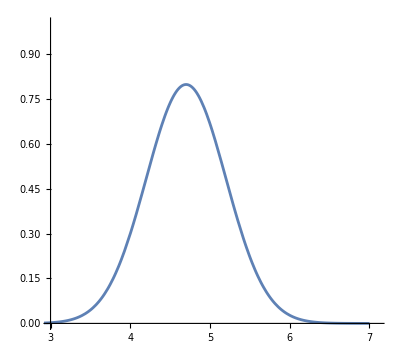

```mathematica
likelihood[m_]:=gaussian[4.7, m,0.5];
Plot[likelihood[m], {m, 0, 7}, PlotRange->{{3, 7.1},{0,1.0}}, AspectRatio->0.9]
```

### Step 4 — Tabulate the Product of the Likelihood and the Prior

In Step 2, you tabulated the likelihood. Take a look at the graph of the prior. It is 0 unless m is between 4 and 6. If m is between 4 and 6, it is 1/2. Using these facts, you should be able to quickly tabulate the product of the likelihood and the prior.

```mathematica
prior[m_]:=If[4<=m<=6,0.5,0];
product[m_]:=likelihood[m]*prior[m];TableForm[Table[{m,product[m]}, {m, 3, 7, 0.5}], TableHeadings->{None, {"m", "P(data|m)*P(m)"}}]
```

m | P(data|m)*P(m)
3. | 0.
3.5 | 0.
4. | 0.149727
4.5 | 0.36827
5. | 0.333225
5.5 | 0.110921
6. | 0.013583
6.5 | 0.
7. | 0.

### Step 5 — Plot the Product of the Likelihood and the Prior

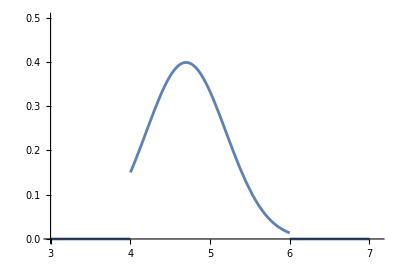

```mathematica
Plot[product[m],{m,3,7}, PlotRange->{{3,7.1},{0,0.5}}, AspectRatio->2/3]
```

### Step 6 — Do the Integral in the Denominator

I have mentioned many times that Mathematica is pretty good at doing integrals. Instead of doing our own estimate, let’s make Mathematica do this one:

```mathematica
denominator = Integrate[product[m],{m,4,6}]
```

0.457291

### Step 7 — Tabulate the Posterior

You need to use the results of Steps 4 and 6 to tabulate the posterior. You just need to divide what you got in Step 4 by what Mathematica got in Step 6.

```mathematica
posterior[m_]:=product[m]/denominator;
TableForm[Table[{m,posterior[m]}, {m, 3, 7, 0.5}], TableHeadings->{None, {"m", "P(m|data)=(P (data | m)*P (m))/denominator"}}]
```

m | P(m|data)=(P (data | m)*P (m))/denominator
3. | 0.
3.5 | 0.
4. | 0.327423
4.5 | 0.80533
5. | 0.728693
5.5 | 0.242561
6. | 0.0297031
6.5 | 0.
7. | 0.

### Step 8 — Plot the Posterior

In Step 7, you tabulated the posterior. Now you are going to plot it.

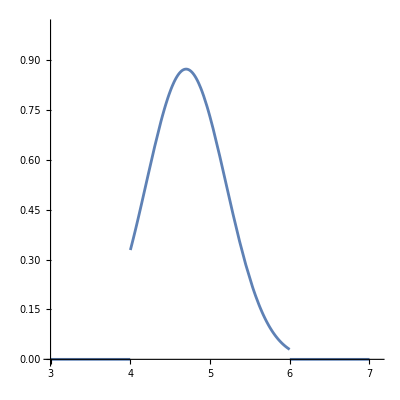

```mathematica
Plot[posterior[m],{m,3,7}, PlotRange->{{3,7.1},{0,1.0}}, AspectRatio->1]
```

### Step 9 — Interpret the Posterior

(a) What would you estimate that the probability is that the bacterium’s survival time is between 4.5 and 5 hours? Shade the region of the graph that answers this question in addition to estimating the answer.

Since I have invested a lot of time in getting good with Mathematica, I will just unleash it to get the answer instead of doing the requested shading.

```mathematica
Integrate[posterior[m],{m, 4.5, 5}]
```

0.416768

So about 42%.

(b) Unleash Mathematica again, this time on the range 5.5 to 5.6

```mathematica
Integrate[posterior[m],{m, 5.5, 5.6}]
```

0.0206312

So about 2%.

(c) For what two reasons was your answer to (b) smaller than your answer to (a)?

Not only is the posterior lower in this region, but the range of values we considered in (b) was smaller than the range of values we considered in (b)